```mathematica
Clear[p,f,x,w]
```

```mathematica
(* Modulo two pattern the same: Minimal Pisot Pattern fractal:even-even*)
```

```mathematica
p={x^3-x-1,1-2 x-2 x^2+x^3,1-4 x-4 x^2+x^3,1-6 x-6 x^2+x^3}
```

{-1-x+x^3,1-2 x-2 x^2+x^3,1-4 x-4 x^2+x^3,1-6 x-6 x^2+x^3}

```mathematica
Table[x/.NSolve[p[[i]]==0,x],{i,Length[p]}]
```

{{-0.662359-0.56228 ⅈ,-0.662359+0.56228 ⅈ,1.32472},{-1.,0.381966,2.61803},{-1.,0.208712,4.79129},{-1.,0.145898,6.8541}}

```mathematica
w=Table[x/.NSolve[p[[i]]==0,x][[3]],{i,Length[p]}]
```

{1.32472,2.61803,4.79129,6.8541}

```mathematica
f[x_]=Fit[w,{1,x},x]
```

-0.793316+1.87614 x

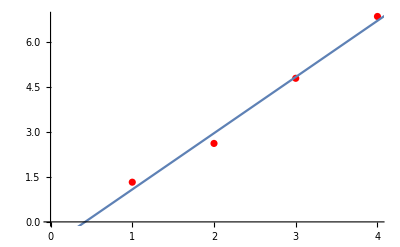

```mathematica
Show[ListPlot[w,PlotStyle->Red],Plot[f[x],{x,0,9}]]
```